# Versuch 49

```mathematica
ClearAll["Global`*"]
```

## Einstellungen

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
legendSettings={LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}};
```

## Formattierung

```mathematica
f[{a_,b_}]:=TeXForm@NumberForm[SetAccuracy[a±b,Accuracy@SetPrecision[b,2]],ExponentFunction->(Null&)]//ToString//Quiet
```

## Fehlerrechnung

```mathematica
errorVolt[reading_,range_]:=If[range==1,0.025Abs[reading]/100+0.006range/100,If[range==10,0.025Abs[reading]/100+0.005range/100,If[range==100,0.025Abs[reading]/100+0.005range/100,If[range==1000,0.025Abs[reading]/100+0.005range/100]]]]
```

```mathematica
errorCurrent[reading_,range_]:=If[range==10,0.05Abs[reading]/100+0.015range/100,If[range==100,0.05Abs[reading]/100+0.005range/100]]
```

## Gaussgewichtete Regression

```mathematica
gaussReg[xdata_,ydata_,dydata_]:=With[{Δ=Total[1/#^2&/@ dydata]Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[xdata]}]-(Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[xdata]}])^2},{1/Δ(Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}] Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), 1/Δ(Total[1/#^2&/@ dydata]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), Sqrt[1/Δ Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]], Sqrt[1/Δ Total[1/#^2&/@ dydata]]} ]
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

```mathematica
combinedReg[xdata_,ydata_,dydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σa,σb,σ},Δ=(n sx2-sx^2);{a,b,σa,σb}=gaussReg[xdata,ydata, dydata];σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,Max[σa,σ Sqrt[sx2/Δ]],Max[σb,σ Sqrt[n/Δ]]}]
```

## Schottky-Langmuir-Raumladungsgesetz

```mathematica
rawData65=SortBy[Import[NotebookDirectory[]<>"Anodenstrom Uh 6.5 V.xlsx"][[1]],First];
```

```mathematica
data65=rawData65[[All,1;;2]];
```

```mathematica
rawData75=SortBy[Import[NotebookDirectory[]<>"Anodenstrom Uh 7.5 V.xlsx"][[1]],First];
```

```mathematica
data75=rawData75[[All,1;;2]];
```

```mathematica
rawData75[[-1]]
```

{500.15,13.075,1000.,100.}

```mathematica
yerror65=Table[errorCurrent[rawData65[[i,2]],Round[rawData65[[i,4]]]],{i,1,Length[rawData65]}];
yerror75=Table[errorCurrent[rawData75[[i,2]],Round[rawData75[[i,4]]]],{i,1,Length[rawData75]}];
```

```mathematica
xerror65=Table[errorVolt[rawData65[[i,1]],Round[rawData65[[i,3]]]],{i,1,Length[rawData65]}];
xerror75=Table[errorVolt[rawData75[[i,1]],Round[rawData75[[i,3]]]],{i,1,Length[rawData75]}];
```

### Abb 3

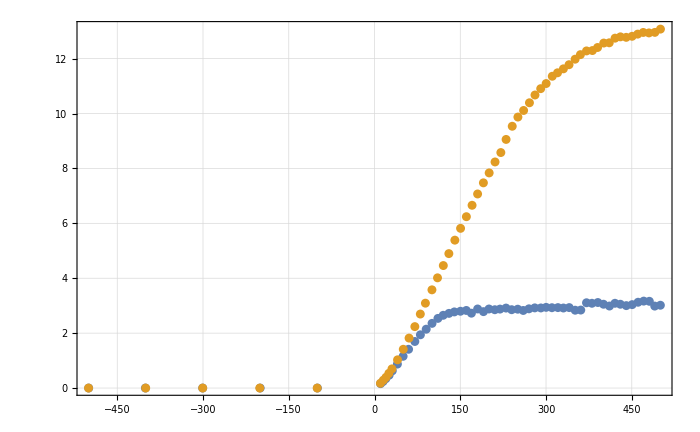

```mathematica
ListPlot[{Table[{Around[data65[[i,1]],xerror65[[i]]],Around[data65[[i,2]],yerror65[[i]]]},{i,1,Length[data65]}],Table[{Around[data75[[i,1]],xerror75[[i]]],Around[data75[[i,2]],yerror75[[i]]]},{i,1,Length[data75]}]},pltsettings,PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"fig3.pdf",ListPlot[{Table[{Around[data65[[i,1]],xerror65[[i]]],Around[data65[[i,2]],yerror65[[i]]]},{i,1,Length[data65]}],Table[{Around[data75[[i,1]],xerror75[[i]]],Around[data75[[i,2]],yerror75[[i]]]},{i,1,Length[data75]}]},pltsettings,PlotRange->All],Background->None];
```

### Cut The Data!!!!

```mathematica
cutData65=DeleteCases[data65,x_/;x[[1]]<0];
cutData75=DeleteCases[data75,x_/;x[[1]]<0];
```

```mathematica
cutyError65=yerror65[[-Length[cutData65];;-1]];
cutyError75=yerror75[[-Length[cutData75];;-1]];
```

```mathematica
cutxError65=xerror65[[-Length[cutData65];;-1]];
cutxError75=xerror75[[-Length[cutData75];;-1]];
```

### Abb. 4

The error in y^(2/3) is given by
Δy^(2/3)=2/3 y^(-2/3) Δy

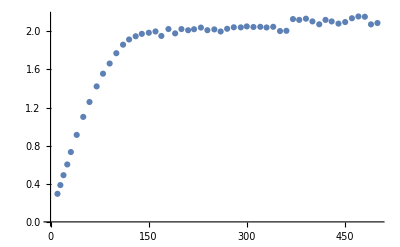

```mathematica
ListPlot[{#[[1]],#[[2]]^(2/3)}&/@cutData65]
```

```mathematica
reg1Cut=8;
```

```mathematica
pars1=gaussReg[cutData65[[1;;reg1Cut,1]],cutData65[[1;;reg1Cut,2]]^(2/3), cutyError65[[1;;reg1Cut]]]
```

{0.0904225,0.0201034,0.0013348,0.0000418821}

```mathematica
pars12=ungewichteterReg[cutData65[[1;;reg1Cut,1]],cutData65[[1;;reg1Cut,2]]^(2/3)]
```

{0.0948212,0.0199564,0.0128846,0.000364336}

```mathematica
pars13=combinedReg[cutData65[[1;;reg1Cut,1]],cutData65[[1;;reg1Cut,2]]^(2/3), cutyError65[[1;;reg1Cut]]]
```

{0.0904225,0.0201034,0.0130599,0.000369295}

```mathematica
f[{-pars13[[1]]/pars13[[2]], Sqrt[(pars13[[3]]/pars13[[2]])^2 + (pars13[[1]]/pars13[[2]]^2 pars13[[4]])^2]}]
```

-4.50\pm 0.65

```mathematica
LinearModelFit[Transpose[{cutData65[[1;;reg1Cut,1]],cutData65[[1;;reg1Cut,2]]^(2/3)}], x,x,Weights->1/cutyError65[[1;;reg1Cut]]^2]
```

FittedModel[…]

```mathematica
LinearModelFit[Transpose[{cutData65[[1;;reg1Cut,1]],cutData65[[1;;reg1Cut,2]]^(2/3)}], x,x,Weights->1/cutyError65[[1;;reg1Cut]]^2]["RSquared"]
```

0.998154

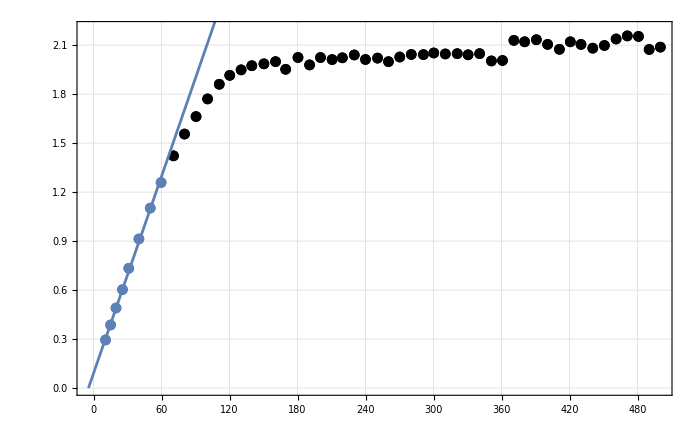

```mathematica
Show[ListPlot[Table[{{Around[cutData65⟦i,1⟧,cutxError65[[i]]],Around[cutData65⟦i,2⟧^(2/3),(2 cutyError65⟦i⟧)/(3 cutData65⟦i,2⟧^(2/3))]}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],Plot[pars1⟦1⟧+pars1⟦2⟧ x,{x,-pars1[[1]]/pars1[[2]],500}],pltsettings,PlotRange->{All,{0,2.2}}]
```

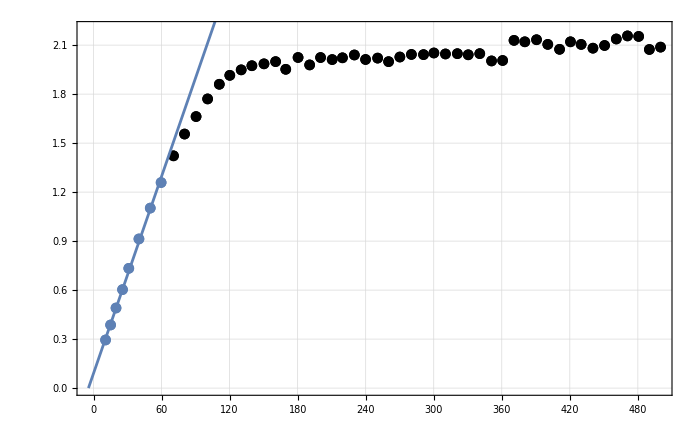

```mathematica
Show[ListPlot[Table[{{cutData65⟦i,1⟧,cutData65⟦i,2⟧^(2/3)}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],Plot[pars1⟦1⟧+pars1⟦2⟧ x,{x,-pars1[[1]]/pars1[[2]],500}],pltsettings,PlotRange->{All,{0,2.2}}]
```

```mathematica
Export[NotebookDirectory[]<>"fig4.pdf",Show[ListPlot[Table[{{cutData65⟦i,1⟧,cutData65⟦i,2⟧^(2/3)}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],Plot[pars1⟦1⟧+pars1⟦2⟧ x,{x,-pars1[[1]]/pars1[[2]],500}],pltsettings,PlotRange->{All,{0,2.2}}],Background->None];
```

### Abb. 5

The error in y^(2/3) is given by
Δy^(2/3)=2/3 y^(-2/3) Δy

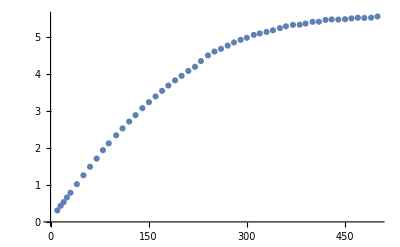

```mathematica
ListPlot[{#[[1]],#[[2]]^(2/3)}&/@cutData75]
```

```mathematica
reg2Cut=11;
```

```mathematica
pars2=gaussReg[cutData75[[1;;reg2Cut,1]],cutData75[[1;;reg2Cut,2]]^(2/3), cutyError75[[1;;reg2Cut]]]
```

{0.0750073,0.0232524,0.00115006,0.0000268533}

```mathematica
pars23=combinedReg[cutData75[[1;;reg2Cut,1]],cutData75[[1;;reg2Cut,2]]^(2/3), cutyError75[[1;;reg2Cut]]]
```

{0.0750073,0.0232524,0.00619968,0.000119859}

```mathematica
f[{pars23[[1]],pars23[[3]]}]
f[{pars23[[2]],pars23[[4]]}]
```

0.0750\pm 0.0062

0.02325\pm 0.00012

```mathematica
f[{-pars23[[1]]/pars23[[2]], Sqrt[(pars23[[3]]/pars23[[2]])^2 + (pars23[[1]]/pars23[[2]]^2 pars23[[4]])^2]}]
```

-3.23\pm 0.27

```mathematica
LinearModelFit[Transpose[{cutData75[[1;;reg2Cut,1]],cutData75[[1;;reg2Cut,2]]^(2/3)}],x,x,Weights->1/cutyError75[[1;;reg2Cut]]^2]
```

FittedModel[…]

```mathematica
LinearModelFit[Transpose[{cutData75[[1;;reg2Cut,1]],cutData75[[1;;reg2Cut,2]]^(2/3)}],x,x,Weights->1/cutyError75[[1;;reg2Cut]]^2]["RSquared"]
```

0.999797

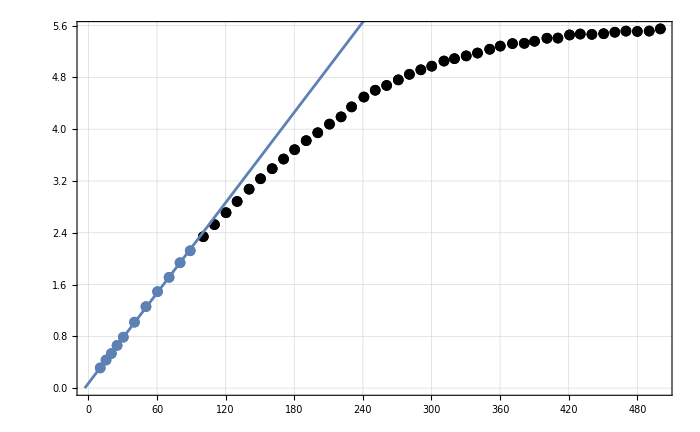

```mathematica
Show[ListPlot[Table[{{Around[cutData75⟦i,1⟧,cutxError75[[i]]],Around[cutData75⟦i,2⟧^(2/3),(2 cutyError75⟦i⟧)/(3 cutData75⟦i,2⟧^(2/3))]}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],Plot[pars2⟦1⟧+pars2⟦2⟧ x,{x,-pars2[[1]]/pars2[[2]],500}],pltsettings]
```

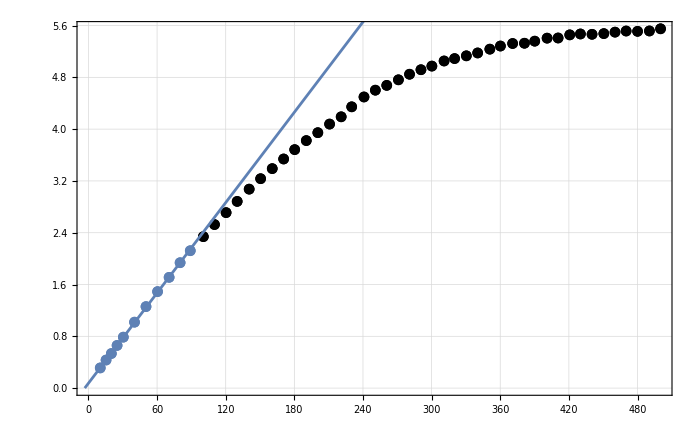

```mathematica
Show[ListPlot[Table[{{cutData75⟦i,1⟧,cutData75⟦i,2⟧^(2/3)}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],Plot[pars2⟦1⟧+pars2⟦2⟧ x,{x,-pars2[[1]]/pars2[[2]],500}],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"fig5.pdf",Show[ListPlot[Table[{{cutData75⟦i,1⟧,cutData75⟦i,2⟧^(2/3)}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],Plot[pars2⟦1⟧+pars2⟦2⟧ x,{x,-pars2[[1]]/pars2[[2]],500}],pltsettings],Background->None];
```

### Abb 6

```mathematica
logData65=Log[cutData65]
```

{{2.36029,-1.83258},{2.71051,-1.42587},{2.98669,-1.06857},{3.24083,-0.758646},{3.43637,-0.465534},{3.68948,-0.136049},{3.91242,0.14583},{4.08755,0.345007},{4.25594,0.528273},{4.38523,0.662688},{4.50447,0.762533},{4.61116,0.856965},{4.70876,0.931061},{4.78874,0.97456},{4.86915,1.00063},{4.939,1.01997},{5.0127,1.02873},{5.07861,1.03893},{5.13285,1.0032},{5.19495,1.05779},{5.25002,1.02371},{5.29932,1.05762},{5.34925,1.04837},{5.39135,1.0564},{5.43812,1.06918},{5.48018,1.04872},{5.52358,1.05501},{5.56137,1.03886},{5.59887,1.05994},{5.63586,1.07158},{5.67329,1.07076},{5.70425,1.07814},{5.73764,1.07374},{5.77094,1.075},{5.80033,1.07004},{5.83065,1.07517},{5.86076,1.04211},{5.88821,1.04416},{5.91566,1.13346},{5.94099,1.12736},{5.96781,1.13633},{5.99286,1.11609},{6.0185,1.09444},{6.04166,1.12736},{6.06376,1.11593},{6.08766,1.09945},{6.11069,1.1113},{6.13338,1.13953},{6.15458,1.15266},{6.17528,1.15048},{6.19471,1.0937},{6.21465,1.1041}}

```mathematica
dlogx65=Table[cutxError65[[i]]/cutData65[[i,1]],{i,1,Length[cutData65]}];
dlogy65=Table[cutyError65[[i]]/cutData65[[i,2]],{i,1,Length[cutData65]}]
```

{0.009875,0.0067422,0.00486681,0.00370307,0.0028893,0.00221861,0.00179646,0.00156232,0.00138443,0.0012732,0.00119972,0.00113667,0.0010912,0.00106604,0.00105147,0.00104091,0.00103619,0.00103075,0.00105006,0.00102083,0.00103889,0.00102092,0.00102576,0.00102156,0.00101493,0.00102558,0.00102228,0.00103079,0.00101971,0.0010137,0.00101412,0.00101034,0.00101259,0.00101195,0.00101449,0.00101186,0.00102906,0.00102798,0.000982874,0.00098583,0.000981495,0.000991336,0.00100209,0.00098583,0.000991417,0.000999584,0.000993697,0.000979954,0.000973694,0.000974729,0.00100246,0.000997265}

```mathematica
pars3=gaussReg[logData65[[1;;reg1Cut,1]],logData65[[1;;reg1Cut,2]],dlogy65[[1;;reg1Cut]]]
```

{-4.88048,1.28155,0.00968145,0.00255166}

```mathematica
pars33=combinedReg[logData65[[1;;reg1Cut,1]],logData65[[1;;reg1Cut,2]],dlogy65[[1;;reg1Cut]]]
```

{-4.88048,1.28155,0.0460678,0.0137518}

```mathematica
f[{pars33[[1]],pars33[[3]]}]
f[{pars33[[2]],pars33[[4]]}]
```

-4.880\pm 0.046

1.282\pm 0.014

```mathematica
LinearModelFit[logData65[[1;;reg1Cut]],x,x,Weights->1/dlogy65[[1;;reg1Cut]]^2]
```

FittedModel[…]

```mathematica
LinearModelFit[logData65[[1;;reg1Cut]],x,x,Weights->1/dlogy65[[1;;reg1Cut]]^2]["RSquared"]
```

0.998894

```mathematica
cutData65[[1]]
cutData65[[-1]]
```

{10.594,0.16}

{500.02,3.0165}

```mathematica
pars3[[2]]
```

1.28155

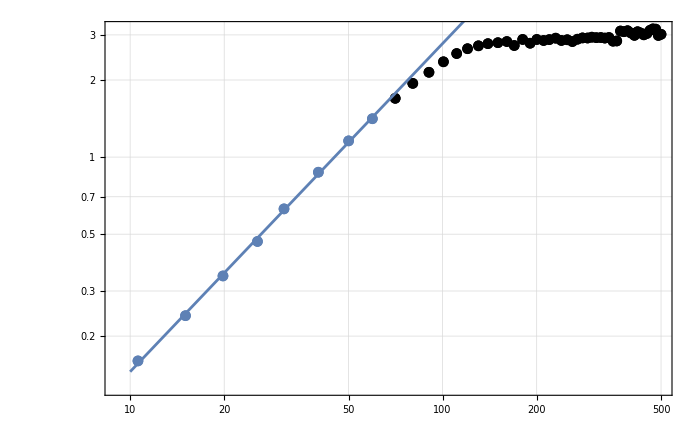

```mathematica
Show[ListLogLogPlot[Table[{{Around[cutData65⟦i,1⟧,cutxError65[[i]]],Around[cutData65⟦i,2⟧,cutyError65⟦i⟧]}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],LogLogPlot[E^pars3[[1]] x^(pars3[[2]]),{x,10,500}],pltsettings]
```

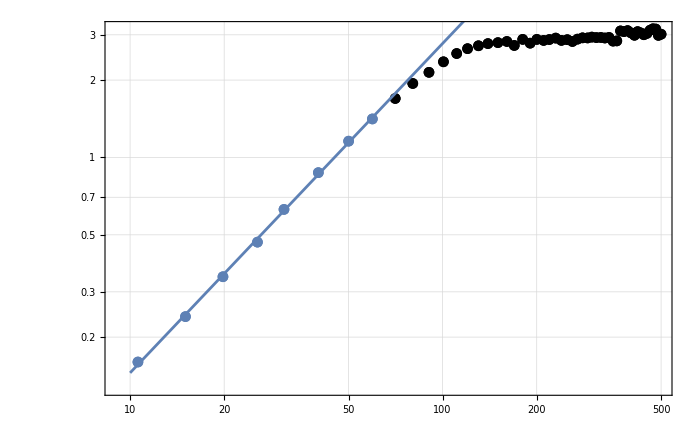

```mathematica
Show[ListLogLogPlot[Table[{{cutData65⟦i,1⟧,cutData65⟦i,2⟧}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],LogLogPlot[E^pars3[[1]] x^(pars3[[2]]),{x,10,500}],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"fig6.pdf",Show[ListLogLogPlot[Table[{{cutData65⟦i,1⟧,cutData65⟦i,2⟧}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],LogLogPlot[E^pars3[[1]] x^(pars3[[2]]),{x,10,500}],pltsettings],Background->None];
```

### Abb 7

```mathematica
logData75=Log[cutData75];
```

```mathematica
dlogx75=Table[cutxError75[[i]]/cutData75[[i,1]],{i,1,Length[cutData75]}];
dlogy75=Table[cutyError75[[i]]/cutData75[[i,2]],{i,1,Length[cutData75]}];
```

```mathematica
pars4=gaussReg[logData75[[1;;reg2Cut,1]],logData75[[1;;reg2Cut,2]],dlogy75[[1;;reg2Cut]]]
```

{-5.06136,1.37937,0.00592883,0.00141096}

```mathematica
pars43=combinedReg[logData75[[1;;reg2Cut,1]],logData75[[1;;reg2Cut,2]],dlogy75[[1;;reg2Cut]]]
```

{-5.06136,1.37937,0.0547718,0.0149683}

```mathematica
f[{pars43[[1]],pars43[[3]]}]
f[{pars43[[2]],pars43[[4]]}]
```

-5.061\pm 0.055

1.379\pm 0.015

```mathematica
LinearModelFit[logData75[[1;;reg2Cut]],x,x,Weights->1/dlogy75[[1;;reg2Cut]]^2]
```

FittedModel[…]

```mathematica
LinearModelFit[logData75[[1;;reg2Cut]],x,x,Weights->1/dlogy75[[1;;reg2Cut]]^2]["RSquared"]
```

0.99974

```mathematica
cutData75[[1]]
cutData75[[-1]]
```

{10.3273,0.174}

{500.15,13.075}

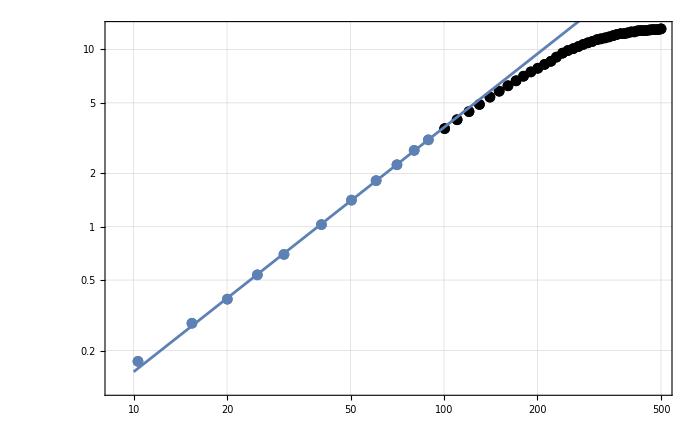

```mathematica
Show[ListLogLogPlot[Table[{{Around[cutData75⟦i,1⟧,cutxError75[[i]]],Around[cutData75⟦i,2⟧,cutyError75⟦i⟧]}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],LogLogPlot[E^pars4[[1]] x^(pars4[[2]]),{x,10,500}],pltsettings]
```

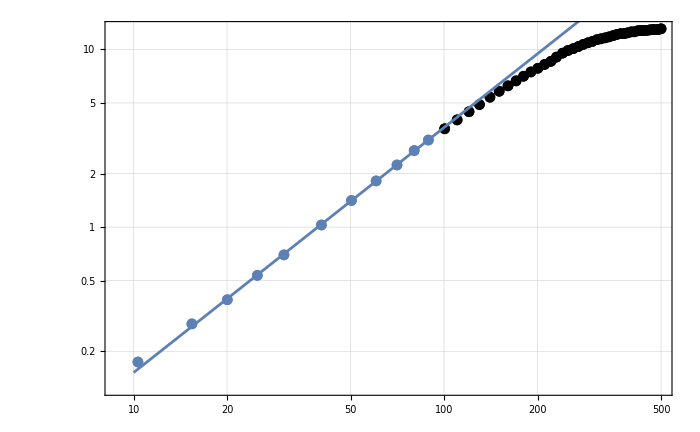

```mathematica
Show[ListLogLogPlot[Table[{{cutData75⟦i,1⟧,cutData75⟦i,2⟧}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],LogLogPlot[E^pars4[[1]] x^(pars4[[2]]),{x,10,500}],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"fig7.pdf",Show[ListLogLogPlot[Table[{{cutData75⟦i,1⟧,cutData75⟦i,2⟧}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],LogLogPlot[E^pars4[[1]] x^(pars4[[2]]),{x,10,500}],pltsettings],Background->None];
```

### Abb 8

d(Temperature) = 97 d(Uh)
d(I/T^2) = ( (dI/T^2)^2 + (2I/T^3 dT)^2 )^(1/2)

```mathematica
Temp[Uh_]:=1616+97 Uh
```

```mathematica
rawDataTemp=Import[NotebookDirectory[]<>"Temperaturabhangigkeit.xlsx"][[1]];
```

```mathematica
dataTemp={#[[1]],#[[2]]*10^(-3)}&/@rawDataTemp[[All,1;;2]]
```

{{5.0047,0.0002227},{5.1022,0.0002896},{5.2041,0.0003501},{5.3012,0.0004115},{5.4002,0.0004892},{5.4923,0.000574},{5.6031,0.0007224},{5.7004,0.0008576},{5.8051,0.0010471},{5.9057,0.0012392},{6.0172,0.0015024},{6.1038,0.0017461},{6.2007,0.0020452},{6.3025,0.0024321},{6.4026,0.0028259},{6.5021,0.0032513},{6.6001,0.0037672},{6.7067,0.004382},{6.8021,0.0050954},{6.9001,0.0058175},{7.003,0.0067463}}

```mathematica
dUhdataTemp=Table[errorVolt[rawDataTemp[[i,1]],Round[rawDataTemp[[i,3]]]],{i,1,Length[rawDataTemp]}];
dIdataTemp=10^(-3)*Table[errorCurrent[rawDataTemp[[i,2]],Round[rawDataTemp[[i,4]]]],{i,1,Length[rawDataTemp]}];
```

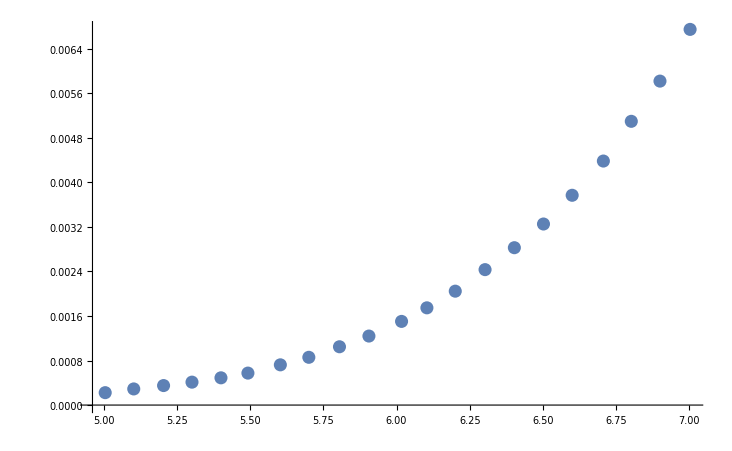

```mathematica
ListPlot[Table[{Around[dataTemp[[i,1]],dUhdataTemp[[i]]],Around[dataTemp[[i,2]],dIdataTemp[[i]]]},{i,1,Length[dataTemp]}]]
```

```mathematica
ydataTemp=#[[2]]/Temp[#[[1]]]^2&/@dataTemp;
```

```mathematica
dydataTemp=Table[(dIdataTemp⟦i⟧/Temp[dataTemp⟦i,1⟧]^2)^2 + (((2 dataTemp⟦i,2⟧) (97 dUhdataTemp⟦i⟧))/Temp[dataTemp⟦i,1⟧]^3)^2,{i,1,Length[ydataTemp]}];
```

```mathematica
logydataTemp=Log[ydataTemp];
```

```mathematica
dlogydataTemp=Table[dydataTemp[[i]]/ydataTemp[[i]],{i,1,Length[ydataTemp]}]
```

{2.64141×10^-15,2.09819×10^-15,1.78394×10^-15,1.56067×10^-15,1.36179×10^-15,1.20849×10^-15,1.03277×10^-15,9.27541×10^-16,8.302×10^-16,7.64653×10^-16,7.06856×10^-16,6.72831×10^-16,6.46152×10^-16,6.27415×10^-16,6.18748×10^-16,6.16992×10^-16,6.22301×10^-16,6.34788×10^-16,6.55442×10^-16,6.79481×10^-16,7.14499×10^-16}

```mathematica
xdataTemp=1/(Temp/@dataTemp[[All,1]]);
```

```mathematica
dxdataTemp=Table[(97 dUhdataTemp⟦i⟧)/Temp[dataTemp⟦i,1⟧]^2,{i,1,Length[dataTemp]}]
```

{3.84646×10^-8,3.86513×10^-8,3.88412×10^-8,3.90174×10^-8,3.91923×10^-8,3.93508×10^-8,3.95363×10^-8,3.96945×10^-8,3.98601×10^-8,4.00146×10^-8,4.01809×10^-8,4.03065×10^-8,4.04434×10^-8,4.05832×10^-8,4.07168×10^-8,4.08457×10^-8,4.09691×10^-8,4.10993×10^-8,4.12125×10^-8,4.13253×10^-8,4.14404×10^-8}

```mathematica
pars5=gaussReg[xdataTemp, logydataTemp, dlogydataTemp]
```

{13.5415,-77987.2,8.5214×10^-15,1.89714×10^-11}

```mathematica
pars53=combinedReg[xdataTemp, logydataTemp, dlogydataTemp]
```

{13.5415,-77987.2,0.38162,838.007}

```mathematica
f[{pars53[[1]],pars53[[3]]}]
f[{pars53[[2]],pars53[[4]]}]
```

13.54\pm 0.38

-77990.\pm 840.

```mathematica
fit=LinearModelFit[Transpose[{xdataTemp, logydataTemp}],x,x,Weights->1/dlogydataTemp^2]
```

FittedModel[…]

```mathematica
fit["RSquared"]
```

0.998479

```mathematica
kB=1.38*10^(-23);
qe=1.6*10^(-19);
```

```mathematica
pars53[[2]]kB
pars53[[4]]kB
```

-1.07622×10^-18

1.15645×10^-20

```mathematica
f[{-pars53[[2]]kB/qe,pars53[[4]]kB/qe}]
```

6.726\pm 0.072

```mathematica
LinearModelFit[Transpose[{xdataTemp,Log@ydataTemp}],x,x]
```

FittedModel[…]

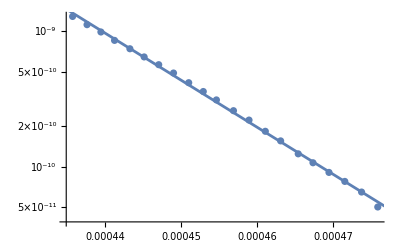

```mathematica
Show[ListLogPlot[Transpose[{xdataTemp,ydataTemp}]],LogPlot[Exp[fit[x]],{x,0,1}]]
```

```mathematica
dlogydataTemp
```

{2.64141×10^-15,2.09819×10^-15,1.78394×10^-15,1.56067×10^-15,1.36179×10^-15,1.20849×10^-15,1.03277×10^-15,9.27541×10^-16,8.302×10^-16,7.64653×10^-16,7.06856×10^-16,6.72831×10^-16,6.46152×10^-16,6.27415×10^-16,6.18748×10^-16,6.16992×10^-16,6.22301×10^-16,6.34788×10^-16,6.55442×10^-16,6.79481×10^-16,7.14499×10^-16}

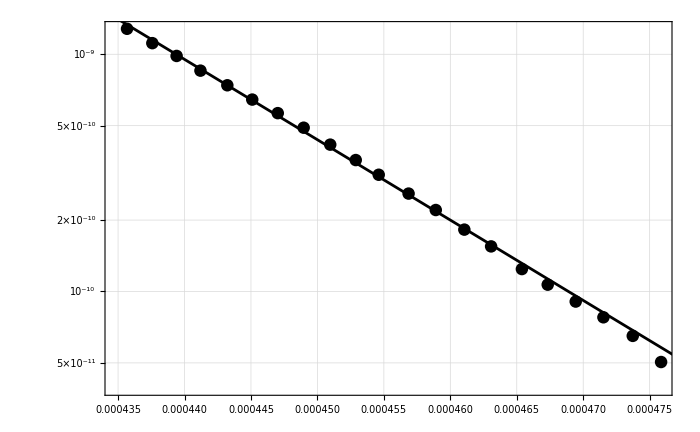

```mathematica
Show[ListLogPlot[Transpose[{xdataTemp,ydataTemp}],PlotStyle->Black],LogPlot[Exp[fit[x]],{x,0,1},PlotStyle->Black],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"fig8.pdf",Show[ListLogPlot[Transpose[{10^4 xdataTemp,10^9 ydataTemp}],PlotStyle->Black],LogPlot[10^9Exp[fit[10^(-4)x]],{x,0,5},PlotStyle->Black],pltsettings],Background->None];
```